```mathematica
$LoadAddOns={"FeynArts"};
```

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.9 (23 Sep 2015) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Loading Models.

To Load Models Inside FeynArts Models directory

```mathematica
FAPatch[PatchModelsOnly->True];
```

Successfully patched FeynArts.

FeynArts directory is

```mathematica
FAdir=$FeynArtsDirectory
```

/Users/aneekphys/Library/Mathematica/Applications/FeynCalc/FeynArts

This will open the Models directory within FeynArts directory.

```mathematica
Run[StringRiffle[{"open",StringJoin[FAdir,"/Models"]}," "]]
```

0

Just Copy Paste the .mod and .gen files generated by FeynRules. Then do,

```mathematica
FAPatch[PatchModelsOnly->True];
```

Successfully patched FeynArts.

Now the model files generated by FeynRules are ready to be used by FeynArts and FeynCalc.

## Some Formalities

```mathematica
(*Give appropriate names*)
```

```mathematica
modelFileName="model_name.mod";
genericFileName="generic_file_name.gen";
```

```mathematica
(*Use this to open model files*)
```

```mathematica
openModelFile[fileName_]:=Run[StringRiffle[{"open",StringJoin[FAdir,"/Models","/",fileName]}," "]];
```

```mathematica
(*To get info about model files that exist already*)

Run[StringRiffle[{"open",StringJoin["/Users/aneekphys/Documents/Useful_Documents/Feyn_","/Model_Files_and_Informations.docx"]}," "]];
```

```mathematica
openModelFile["SM.mod"]
```

0

### Some Comments:

### Some Useful Functions:

```mathematica
CharginoRotationRules[matrixP_,matrixN_]:=Module[
{rule1,rule2,rule},
rule1=Table[Symbol[StringJoin["ChPM",ToString[al],"x",ToString[bl]]]->matrixP[[al,bl]],{al,1,2},{bl,1,2}];
rule2=Table[Symbol[StringJoin["ChNM",ToString[al],"x",ToString[bl]]]->matrixN[[al,bl]],{al,1,2},{bl,1,2}];

rule=Flatten[Join[rule1,rule2]]

];
NeutralinoRotationRules[matrix_]:=Module[
{rule2,rule},
rule2=Table[Symbol[StringJoin["Neu0M",ToString[al],"x",ToString[bl]]]->matrix[[al,bl]],{al,1,4},{bl,1,4}];

Flatten[rule2]
];
```

```mathematica
CharginoMassMatrix={{M2,el/sw v1},{el/sw v2, muH}};
NeutralinoMassMatrix={{M1,0,-el v1/(Sqrt[2]cw),el v2/(Sqrt[2]cw)},{0,M2,el v1/(Sqrt[2]sw),-el v1/(Sqrt[2]sw)},{-el v1/(Sqrt[2]cw),el v1/(Sqrt[2]sw),0,-muH},{el v2/(Sqrt[2]cw),-el v2/(Sqrt[2]sw),-muH,0}};
```

### Setting Parameter Values

```mathematica
cw = mW/mZ;
sw=Sqrt[1-cw^2];
el=Sqrt[4 Pi α];
v1=cb (2 mZ/el cw sw);
v2=sb(2 mZ/el cw sw);
cb=Cos[β];
sb=Sin[β];
```

```mathematica
mZ=91.19;
mW=80.377;
α=1/137;
β=Pi/4;
M1=30;
M2=70;
muH=400;
```

```mathematica
CharginoMassMatrix
NeutralinoMassMatrix
```

(70 | 113.67
113.67 | 400)

(30 | 0 | -43.0715 | 43.0715
0 | 70 | 80.377 | -80.377
-43.0715 | 80.377 | 0 | -400
43.0715 | -80.377 | -400 | 0)

```mathematica
{NeutralinoMasses,NeutralinoRotationMatrix}=Eigensystem[NeutralinoMassMatrix];
```

```mathematica
NeutralinoMasses
```

{443.56,-400.,47.2471,9.1927}

```mathematica
NeutralinoMasses[[{1,2,3,4}]]=NeutralinoMasses[[{4,3,2,1}]];
NeutralinoRotationMatrix[[All,{1,2,3,4}]]=NeutralinoRotationMatrix[[All,{4,3,2,1}]];
```

```mathematica
NeutralinoRotationMatrix
```

(0.669864 | -0.669864 | -0.288262 | 0.13953
0.707107 | 0.707107 | 5.33464×10^-16 | -2.80627×10^-16
-0.114062 | 0.114062 | -0.805869 | -0.569698
-0.195632 | 0.195632 | -0.517185 | 0.809924)

### Rotation and Mass Rules

```mathematica
neutralinoRotationRules=NeutralinoRotationRules[NeutralinoRotationMatrix]
```

{Neu0M1x1→0.669864,Neu0M1x2→-0.669864,Neu0M1x3→-0.288262,Neu0M1x4→0.13953,Neu0M2x1→0.707107,Neu0M2x2→0.707107,Neu0M2x3→5.33464×10^-16,Neu0M2x4→-2.80627×10^-16,Neu0M3x1→-0.114062,Neu0M3x2→0.114062,Neu0M3x3→-0.805869,Neu0M3x4→-0.569698,Neu0M4x1→-0.195632,Neu0M4x2→0.195632,Neu0M4x3→-0.517185,Neu0M4x4→0.809924}

```mathematica
MNeu1=NeutralinoMasses[[1]];
MNeu2=NeutralinoMasses[[2]];
```

## Decay of Z into two Neutralinos Z -> χ_(0,1)+ χ_(0,1)

```mathematica
t12=CreateTopologies[0,1->2]
```

TopologyList(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(4)),Propagator(Outgoing)(Vertex(1)(2),Vertex(3)(4)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(4))))

> Top. 1: 1 diagram

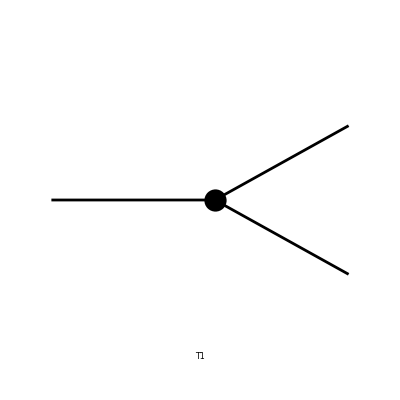

FeynArtsGraphics(1→2)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
Paint[%]
```

```mathematica
Aa=InsertFields[t12,V[2]->{F[7],F[7]},GenericModel->"SUSY_SU(2)_Higgs_3_FA",Model->"SUSY_SU(2)_Higgs_3_FA"];
```

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

> Top. 1: 1 diagram

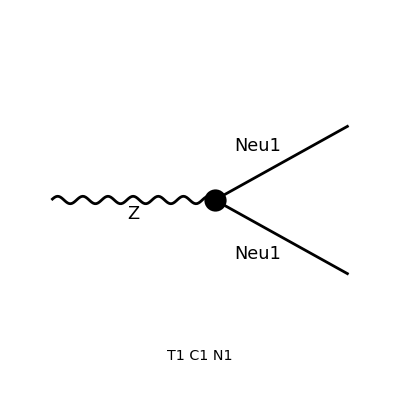

FeynArtsGraphics({Z}→{Neu1,Neu1})(([T1 C1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
Paint[%,PaintLevel->{Classes},ImageSize->{512,512}]
```

```mathematica
InitializeModel["SUSY_SU(2)_Higgs_3_FA",GenericModel->"SUSY_SU(2)_Higgs_3_FA"];
```

loading generic model file /Users/aneekphys/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/SUSY_SU(2)_Higgs_3_FA.gen

> $GenericMixing is OFF

generic model {SUSY_SU(2)_Higgs_3_FA} initialized

loading classes model file /Users/aneekphys/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/SUSY_SU(2)_Higgs_3_FA.mod

> 46 particles (incl. antiparticles) in 25 classes

> $CounterTerms are ON

> 303 vertices

classes model {SUSY_SU(2)_Higgs_3_FA} initialized

```mathematica
feynArtsAmp=CreateFeynAmp[Aa]/.{Mass[F[7],External]->MNeu1,Mass[F[7],External]->MNeu1,RelativeCF->1,G[-1][0][F[7],F[7],V[2]][FANonCommutative[FADiracMatrix[KI1[3]],FAChiralityProjector[-1]]]->(I)*gc294R,G[-1][0][F[7],F[7],V[2]][FANonCommutative[FADiracMatrix[KI1[3]],FAChiralityProjector[1]]]->(I)*gc294L}

InputForm[feynArtsAmp];
```

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

FAFeynAmpList(Process→(V(2) | p1 | FCGV(MZ) | {})→(F(7) | k1 | MNeu1 | {}
F(7) | k2 | MNeu1 | {}),Model→{SUSY_SU(2)_Higgs_3_FA},GenericModel→{SUSY_SU(2)_Higgs_3_FA},AmplitudeLevel→{Generic,Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1),Integral[],-ⅈ ep(V(2),p1,Lor1) ū(k2,MNeu1).(ⅈ gc294R ga(Lor1).(omSubscript[-])+ⅈ gc294L ga(Lor1).(omSubscript[+])).v(k1,MNeu1),{MNeu1,MNeu1,ⅈ gc294R,ⅈ gc294L,1}→Insertions(Classes)({MNeu1,MNeu1,ⅈ gc294L,ⅈ gc294R,1})))

```mathematica
feynCalcAmp=FCFAConvert[feynArtsAmp,IncomingMomenta->{p1},OutgoingMomenta->{k1,k2}];
```

```mathematica
feynCalcAmp//Simplify
```

{-ⅈ (ε̄)^Lor1(p1) (φ(OverBar[k2],MNeu1)).(ⅈ (gc294L (γ̄)^Lor1.(γ̄)^6+gc294R (γ̄)^Lor1.(γ̄)^7)).(φ(-OverBar[k1],MNeu1))}

```mathematica
ampSq=(((feynCalcAmp (ComplexConjugate[feynCalcAmp]))//FeynAmpDenominatorExplicit//FermionSpinSum//DiracSimplify)/.RuleSet1)/.RuleSet2For11//Simplify
```

{-2. (gc294L^2 (MNeu1^2-8315.62)-6. gc294L gc294R MNeu1^2+gc294R^2 (MNeu1^2-8315.62))}

### RuleSets

```mathematica
RuleSet1={Pair[Momentum[Polarization[p1,-I]],Momentum[Polarization[p1,I]]]->-3,Pair[Momentum[k1],Momentum[Polarization[p1,I]]]*Pair[Momentum[k2],Momentum[Polarization[p1,-I]]]->(-Pair[Momentum[k1],Momentum[k2]])+Pair[Momentum[k1],Momentum[p1]]Pair[Momentum[p1],Momentum[k2]]/mZ^2,Pair[Momentum[k2],Momentum[Polarization[p1,I]]]*Pair[Momentum[k1],Momentum[Polarization[p1,-I]]]->(-Pair[Momentum[k1],Momentum[k2]])+Pair[Momentum[k1],Momentum[p1]]Pair[Momentum[p1],Momentum[k2]]/mZ^2,Eps[ind__]->0};
RuleSet2For12={Pair[Momentum[k1],Momentum[p1]]->1/2(mZ^2+MNeu1^2-MNeu2^2),Pair[Momentum[k2],Momentum[p1]]->1/2(mZ^2+MNeu2^2-MNeu1^2),Pair[Momentum[k1],Momentum[k2]]->1/2(mZ^2-MNeu1^2-MNeu2^2)}
RuleSet2For11=RuleSet2For12/.MNeu2->MNeu1
RuleSet3For12={gc295L->(el*(cw^2+sw^2)*(Neu0M3x2*Conjugate[Neu0M3x1]-Neu0M4x2*Conjugate[Neu0M4x1]))/(2*cw*sw),gc295R->-1/2*(el*(cw^2+sw^2)*(Neu0M3x1*Conjugate[Neu0M3x2]-Neu0M4x1*Conjugate[Neu0M4x2]))/(cw*sw)};
RuleSet3For11={gc294L->(el*(cw^2+sw^2)*(Neu0M3x1*Conjugate[Neu0M3x1]-Neu0M4x1*Conjugate[Neu0M4x1]))/(2*cw*sw),gc294R->-1/2*(el*(cw^2+sw^2)*(Neu0M3x1*Conjugate[Neu0M3x1]-Neu0M4x1*Conjugate[Neu0M4x1]))/(cw*sw)};
RuleSet4For12=RuleSet3For12/.neutralinoRotationRules
RuleSet4For11=RuleSet3For11/.neutralinoRotationRules
```

{OverBar[k1]·OverBar[p1]→1/2 (MNeu1^2-MNeu2^2+8315.62),OverBar[k2]·OverBar[p1]→1/2 (-MNeu1^2+MNeu2^2+8315.62),OverBar[k1]·OverBar[k2]→1/2 (-MNeu1^2-MNeu2^2+8315.62)}

{OverBar[k1]·OverBar[p1]→4157.81,OverBar[k2]·OverBar[p1]→4157.81,OverBar[k1]·OverBar[k2]→1/2 (8315.62-2 MNeu1^2)}

{gc295L→0.00918864,gc295R→-0.00918864}

{gc294L→-0.00918864,gc294R→0.00918864}

### Back to Calculation

```mathematica
p12=Sqrt[(mZ^2+MNeu1^2-MNeu2^2)^2/(4 mZ^2)-MNeu1^2];
p11=p12/.MNeu2->MNeu1
```

√(2078.9-MNeu1^2)

```mathematica
DecayRate=1/(64 Pi^2) 4Pi ampSq/mZ^2 p11 //FullSimplify;
```

```mathematica
DecayRate/.Flatten[{RuleSet4For11,MNeu1->NeutralinoMasses[[1]]}]
```

{0.000287857}